```mathematica
stack1 = Graphics[{Darker[Green],Rectangle[{3,0},{2,2}]}]
```

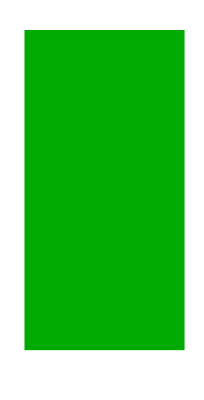

```mathematica
stack2 = Graphics[{Darker[Green],Rectangle[{3,0},{2,2}]}]
```

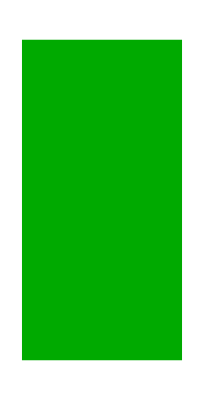

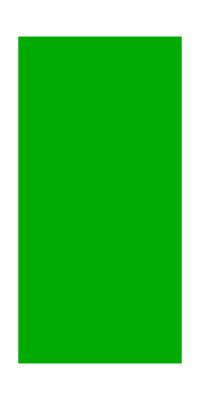

```mathematica
stack3 = Graphics[{Darker[Green],Rectangle[{3,0},{2,2}]}]
```

```mathematica
DynamicModule[{pts={{0,0},{1,1},{2,0},{3,2}}},LocatorPane[Dynamic[pts],Dynamic[Plot[InterpolatingPolynomial[pts,x],{x,0,3},PlotRange->3]]]]
```

```mathematica
ListAnimate[Table[Graphics[Disk[],ImageSize->RandomReal[100]],{50}]]
```

```mathematica
ListAnimate[Table[Graphics[{Darker[Green],Rectangle[{3,0},{2,2}]}],{5}]]
```

```mathematica
FlipView[{stack1,stack2,stack3}]
```

```mathematica
(* Vertical Stack *)
```

```mathematica
list={
Graphics[{Darker[Green],Rectangle[{0,0},{5,10}],Thick,Blue,Disk[{2,3},.1],Blue,Disk[{2,3.5},.1],Thick,Blue,Disk[{2,4},.1],Blue,Disk[{2,4.5},.1],Blue,Disk[{2,5},.1],Blue,Disk[{2,6.5},.1],Blue,Disk[{3,6.5},.1]} ], (* 1 *)
Graphics[{Darker[Green],Rectangle[{0,0},{5,10}],Thick,Blue,Disk[{1,4.5},.1],Blue,Disk[{2,3.5},.1],Thick,Blue,Disk[{2,4},.1],Blue,Disk[{2,4.5},.1],Blue,Disk[{2,5},.1],Blue,Disk[{2,6.5},.1],Blue,Disk[{3,7.5},.1]} ],(* 2 *)
Graphics[{Darker[Green],Rectangle[{0,0},{5,10}],Thick,Blue,Disk[{2,4.5},.1],Blue,Disk[{2,5},.1],Thick,Blue,Disk[{2,4},.1],Blue,Disk[{2,3},.1],Blue,Disk[{2,5},.1],Blue,Disk[{2,7.5},.1],Blue,Disk[{3,7.5},.1]} ],(* 3 *)
Graphics[{Darker[Green],Rectangle[{0,0},{5,10}],Thick,Blue,Disk[{2,3},.1],Blue,Disk[{2,3.5},.1],Thick,Blue,Disk[{2,4},.1],Blue,Disk[{2,4.5},.1],Blue,Disk[{2,5},.1],Blue,Disk[{2,6.5},.1],Blue,Disk[{3,6.5},.1]} ],(* 4 *)
Graphics[{Darker[Green],Rectangle[{0,0},{5,10}],Thick,Blue,Disk[{2,3},.1],Blue,Disk[{2,3.5},.1],Thick,Blue,Disk[{2,4},.1],Blue,Disk[{2,4.5},.1],Blue,Disk[{2,5},.1],Blue,Disk[{2,6.5},.1],Blue,Disk[{3,6.5},.1]} ],(* 5 *)Graphics[{Darker[Green],Rectangle[{0,0},{5,10}],Thick,Blue,Disk[{2,3},.1],Blue,Disk[{2,3.5},.1],Thick,Blue,Disk[{2,4},.1],Blue,Disk[{2,4.5},.1],Blue,Disk[{2,5},.1],Blue,Disk[{2,6.5},.1],Blue,Disk[{3,6.5},.1]} ](* 6 *)
};
ListAnimate[list,AnimationRunning->False]
```

```mathematica
(* ,Thick,Blue,Disk[{1,2},.1] *)
```

```mathematica
(* Graphics 3D Model Frisbee and Field *)
ultimatefrisbeefield = Graphics3D[{
Line[{{-10,-45,-2.44},{-10,45,-2.44}}],(* endzone 1 *)
Line[{{-110,-45,-2.44},{-110,45,-2.44}}],(* endzone 2 *)
Glow[],Darker[Green],EdgeForm[{Thick,Black}],Polygon[{{-120,-45,-2.44},{-120,45,-2.44},{0,45,-2.44},{0,-45,-2.44},{-120,-45,-2.44}}] (* Field *),Cylinder[{{-30,0,-2.4401},{-30,0,-2.44}},2] (* Brick Mark *),
Cylinder[{{-90,0,-2.4401},{-90,0,-2.44}},2] (* Brick Mark *)
}];Show[ultimatefrisbeefield,Boxed->False]
```

-Graphics3D-

```mathematica
(* Field: 70 yards x 40 yards *)
(* End Zone 25 yards deep *)
(* Brick Marks- 18 m from end zone *)
```

-Graphics3D-